```mathematica
(* This Notebook defines modules to find ϕ[n], ϵ[n], η[n], and ns[n]. It does not use the slow roll approx and instead integrates the Klein Gordon equation to find ϕ[n]. It then plots where monomial potentials fall on the r-ns plane. *)
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
(* Define a potential *)
(*v[x_] := x^4*(1-Log[x])*)
v[x_] := x^4
vp[x_]=v'[x]
(* Define a module to find ϕ60 *)
findϕ60 := Module[{ϕ0},
ϕ0 = x /. Last[NSolve[vp[x]==√2*v[x],x]];
Print["ϕ0 = ",ϕ0];
f[t_] = Integrate[v[x]/v'[x],{x,ϕ0,t}];
ϕ60 = t/.Last[NSolve[60==f[t],t]];
Return[ϕ60]] 
ϕ60 = findϕ60
Print["ϕ60 = ",ϕ60]
```

4 x^3

ϕ0 = 2.82843

22.0907

ϕ60 = 22.0907

ϕ0 = 2.82843

{{ϕ→InterpolatingFunction[{{0., 60.}}, <>]}}

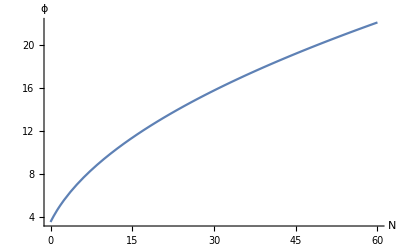

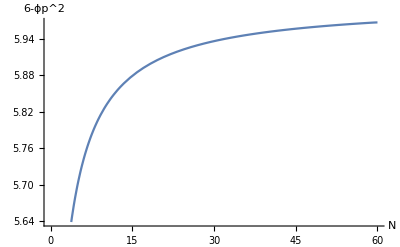

```mathematica
(* Define a module to find ϕ[n] *)
findϕ := Module[{h,hsq,nsr,ϕ60,ϕp60},
(* Define H as a function of number of efolds *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
(* (* Define number of efolds using slow-roll approx *)
nsr[x_] := v[x]/v'[x];(* Strictly speaking, I get the differential form dN=v[x]/v'[x] dx *)
(* find ϕ60, ϕ at n=60 *)
ϕ60 = Evaluate[Last[FindRoot[{nsr[x]-60==0},{x,1}]]]; *)
ϕ60 = findϕ60;
(* find ϕp60 = ϕ'[60] *)
ϕp60 = vp[ϕ60]/v[ϕ60] ;
(* Solve for ϕ[n] *)
(* Note that this form of the differential equation only holds provided: 6-(ϕ'[n])^2≠0. *)NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*v'[ϕ[n]]==0,ϕ[60]==ϕ60,ϕ'[60]==ϕp60},ϕ,{n,60,0},InterpolationOrder->All]]
ϕsol = findϕ
Plot[Evaluate[ϕ[n]/.ϕsol],{n,60,0},AxesLabel->{N,ϕ}]
Plot[Evaluate[6-(ϕ'[n])^2/.ϕsol],{n,60,0},AxesLabel->{N,"6-ϕp^2"}]
```

```mathematica
(* Define a module to find ϕ[n] integrating from ϕ0 instead of ϕ60 *)
findϕUsingϕ0 := Module[{h,hsq,nsr,ϕ0,ϕp0},
(* Define H as a function of number of efolds *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
ϕ0 = x /. Last[NSolve[vp[x]==√2*v[x],x]];
(* find ϕp0 = ϕ'[0] *)
ϕp0 = vp[ϕ0]/v[ϕ0] ;
(* Solve for ϕ[n] *)
(* Note that this form of the differential equation only holds provided: 6-(ϕ'[n])^2≠0. *)NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*v'[ϕ[n]]==0,ϕ[0]==ϕ0,ϕ'[0]==ϕp0},ϕ,{n,0,60},InterpolationOrder->All]]
ϕsol = findϕ
Plot[Evaluate[ϕ[n]/.ϕsol],{n,60,0},AxesLabel->{N,ϕ}]
Plot[Evaluate[6-(ϕ'[n])^2/.ϕsol],{n,60,0},AxesLabel->{N,"6-ϕp^2"}]
```

ϕ0 = 2.82843

{{ϕ→InterpolatingFunction[{{0., 60.}}, <>]}}

-Graphics-

-Graphics-

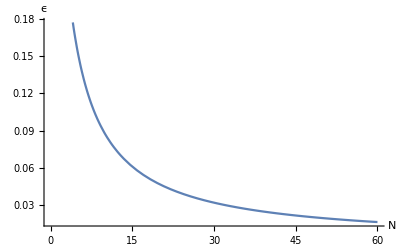

{0.572735}

```mathematica
findϵ := Module[{ϵ},
(* Find ϵ[n] *)
ϵ[n_] := 1/2*D[Log[v[ϕ[n]/.ϕsol]],n];
Return[ϵ[n]]]
ϵ[n_] := findϵ 
Plot[Evaluate[ϵ[n]],{n,60,0},AxesLabel->{N,ϵ}]
ϵ[n]/.{n->0}
```

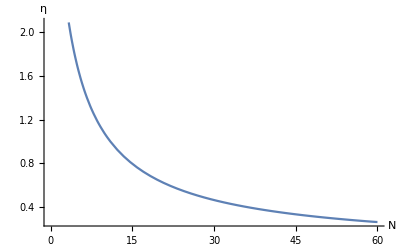

```mathematica
findη := Module[{ϕp,η},
(* Find η[n] *)
ϕp[x_] := v'[x]/v[x];
η[n_] := 1/2*D[Log[vp[ϕ[n]/.ϕsol]]^2,n];
Return[η[n]]]
η[n_] := findη
Plot[Evaluate[η[n]],{n,60,0},AxesLabel->{N,η}]
```

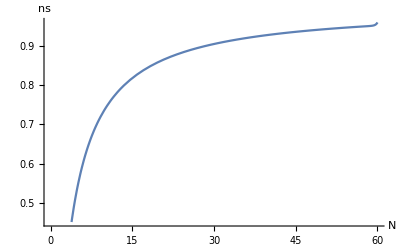

```mathematica
findNs := Module[{ns,ϕ60},
ns[n_] := 1-2*ϵ[n]+D[Log[ϵ[n]],n];
Return[ns[n]]]
ns[n_] := findNs
Plot[Evaluate[ns[n]],{n,60,0},AxesLabel->{N,ns}]
```

{}

p = 2     ϵ[0] = 1.

p = 3     ϵ[0] = 1.

p = 4     ϵ[0] = 1.

p = 5     ϵ[0] = 1.

p = 6     ϵ[0] = 1.

p = 7     ϵ[0] = 1.

p = 8     ϵ[0] = 1.

p = 9     ϵ[0] = 1.

p = 10     ϵ[0] = 1.

p = 11     ϵ[0] = 1.

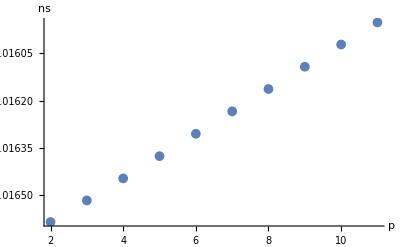

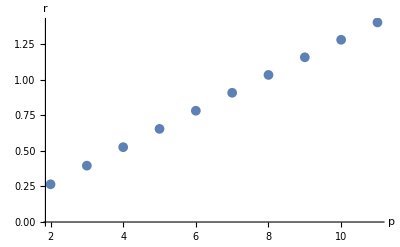

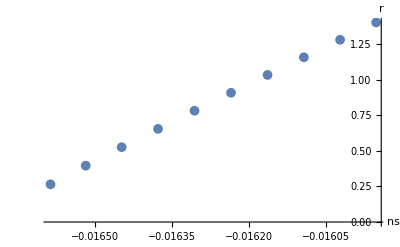

```mathematica
nsList = {}; rList = {};pList = {}
For[p=2,p<12,p++,
Clear[v,ϕsol,ns,ϵ];
v[ϕ_] := ϕ^p;
vp[x_]=v'[x];
ϕsol = findϕUsingϕ0;
ns[n_] = Last[findNs];
ϵ[n_] = Last[findϵ ];
Print["p = ",p,"     ϵ[0] = ",ϵ[n]/.{n->0}];
AppendTo[nsList,ns[n]/.{n->60}];
AppendTo[rList,16*(ϵ[n]/.{n->60})];
AppendTo[pList,p]]
ListPlot[Thread[{pList,nsList}],AxesLabel->{"p",ns},PlotMarkers->{●,10}]
ListPlot[Thread[{pList,rList}],AxesLabel->{"p",r},PlotMarkers->{●,10}]
ListPlot[Thread[{nsList,rList}],AxesLabel->{ns,r},PlotMarkers->{●,10}]
```